# Project: Mode Prop. Wigner Function

## Step-1: Clear everything and make assumptions:

```mathematica
Clear["Global`*"];
SetDirectory["/Users/Sushovit/Documents/GitHub/Mathematica--SU-1-1-/"];
assumpt:={Subscript[x, _]∈Reals,Subscript[p, _]∈Reals,r ∈Reals,r ≥0,θ1 ∈ Reals,0≤θ1≤2π, θ2 ϵ Reals, θ2 ≥ 0,  Subscript[ϕ, _]∈Reals,0≤Subscript[ϕ, _]≤2π,α1 ∈ Reals,α1≥0, α2 ∈ Reals, α2≥0, Γ ϵ Reals, Γ ≥ 0, g ϵ Reals, g ≥ 0}
Refine[ReIm[Subscript[α, 2]],assumpt];
$Assumptions={a<0,a∈Reals,n≥0,n∈Integers};
```

## Step-2: Define operator matrices and mean and covariances here

```mathematica
Subscript[phaseShifter, i_][modeCt_,ϕ_]:=Module[{matrix},
	matrix=IdentityMatrix[2 modeCt];
	Do[
		matrix⟦2i-2+x⟧⟦2i-2+x⟧=Cos[ϕ];
	,{x,1,2}];
	matrix⟦2i⟧⟦2i-1⟧=Sin[ϕ];
	matrix⟦2i-1⟧⟦2i⟧=-Sin[ϕ];
	matrix
];
TMSQZ1[rPump_,θPump_]:=({{Cosh[rPump], 0, Sinh[rPump]Cos[θPump], Sinh[rPump]Sin[θPump]}, {0, Cosh[rPump], Sinh[rPump]Sin[θPump], -Sinh[rPump] Cos[θPump]}, {Sinh[rPump]Cos[θPump], Sinh[rPump]Sin[θPump], Cosh[rPump], 0}, {Sinh[rPump]Sin[θPump], -Sinh[rPump] Cos[θPump], 0, Cosh[rPump]}});
```

## Step-4: Cook up the input state

```mathematica
modeCt=2;

Subscript[means, 1]=Sqrt[2]α1{Cos[θ1],Sin[θ1]};
Subscript[means, 2]=Sqrt[2]α2{Cos[θ2],Sin[θ2]};

X0 :=Flatten[Table[Subscript[means, i],{i,1,modeCt}]] (*input mean*)
MatrixForm[X0=Refine[X0,assumpt]];

Subscript[covMat, 1]=IdentityMatrix[2];
Subscript[covMat, 2]= {{Sin[Γ]^2 Sinh[r]^2+(Cosh[r]+Cos[Γ] Sinh[r])^2,Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r])},{Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r]),Sin[Γ]^2 Sinh[r]^2+(Cosh[r]-Cos[Γ] Sinh[r])^2}};
Γ0 :=Fold[ArrayFlatten[{{#1,0},{0,#2}}]&,Subscript[covMat, 1],Table[Subscript[covMat, i],{i,2,modeCt}]] (*ouptut mean*)
MatrixForm[Γ0=Refine[Γ0,assumpt]];
```

## Step-5: Create the Evolution Matrix

```mathematica
MatrixForm[Sϕ = Refine[Subscript[phaseShifter, 1][2,ϕ], assumpt]]
MatrixForm[SOPA1=TMSQZ1[g,0] ] (*first OPA*)
MatrixForm[SOPA2=TMSQZ1[g,π] ] (*Second OPA*)
MatrixForm[S = SOPA2.Sϕ.SOPA1]
```

(Cos[ϕ] | -Sin[ϕ] | 0 | 0
Sin[ϕ] | Cos[ϕ] | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(Cosh[g] | 0 | Sinh[g] | 0
0 | Cosh[g] | 0 | -Sinh[g]
Sinh[g] | 0 | Cosh[g] | 0
0 | -Sinh[g] | 0 | Cosh[g])

(Cosh[g] | 0 | -Sinh[g] | 0
0 | Cosh[g] | 0 | Sinh[g]
-Sinh[g] | 0 | Cosh[g] | 0
0 | Sinh[g] | 0 | Cosh[g])

(Cos[ϕ] Cosh[g]^2-Sinh[g]^2 | -Cosh[g]^2 Sin[ϕ] | -Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g] | Cosh[g] Sin[ϕ] Sinh[g]
Cosh[g]^2 Sin[ϕ] | Cos[ϕ] Cosh[g]^2-Sinh[g]^2 | Cosh[g] Sin[ϕ] Sinh[g] | Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g]
Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g] | Cosh[g] Sin[ϕ] Sinh[g] | Cosh[g]^2-Cos[ϕ] Sinh[g]^2 | -Sin[ϕ] Sinh[g]^2
Cosh[g] Sin[ϕ] Sinh[g] | -Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g] | Sin[ϕ] Sinh[g]^2 | Cosh[g]^2-Cos[ϕ] Sinh[g]^2)

## Step-6: Get the Output Mean and Covariance

```mathematica
MatrixForm[X2=S.X0](*output mean*) (*This matches with Dong Li paper*)
MatrixForm[Γ2=S.Γ0.Transpose[S]](*output covariance*)
```

(-√2 α1 Cosh[g]^2 Sin[θ1] Sin[ϕ]+√2 α2 Cosh[g] Sin[θ2] Sin[ϕ] Sinh[g]+√2 α2 Cos[θ2] (-Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g])+√2 α1 Cos[θ1] (Cos[ϕ] Cosh[g]^2-Sinh[g]^2)
√2 α1 Cos[θ1] Cosh[g]^2 Sin[ϕ]+√2 α2 Cos[θ2] Cosh[g] Sin[ϕ] Sinh[g]+√2 α2 Sin[θ2] (Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g])+√2 α1 Sin[θ1] (Cos[ϕ] Cosh[g]^2-Sinh[g]^2)
√2 α1 Cosh[g] Sin[θ1] Sin[ϕ] Sinh[g]-√2 α2 Sin[θ2] Sin[ϕ] Sinh[g]^2+√2 α1 Cos[θ1] (Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g])+√2 α2 Cos[θ2] (Cosh[g]^2-Cos[ϕ] Sinh[g]^2)
√2 α1 Cos[θ1] Cosh[g] Sin[ϕ] Sinh[g]+√2 α2 Cos[θ2] Sin[ϕ] Sinh[g]^2+√2 α1 Sin[θ1] (-Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g])+√2 α2 Sin[θ2] (Cosh[g]^2-Cos[ϕ] Sinh[g]^2))

(Cosh[g]^4 Sin[ϕ]^2+(Cos[ϕ] Cosh[g]^2-Sinh[g]^2)^2+Cosh[g] Sin[ϕ] Sinh[g] (Cosh[g] Sin[ϕ] Sinh[g] (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]-Cos[Γ] Sinh[r])^2)+(-Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g]) (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r])))+(-Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g]) (Cosh[g] Sin[ϕ] Sinh[g] (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r]))+(-Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g]) (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]+Cos[Γ] Sinh[r])^2)) | (Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g]) (Cosh[g] Sin[ϕ] Sinh[g] (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]-Cos[Γ] Sinh[r])^2)+(-Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g]) (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r])))+Cosh[g] Sin[ϕ] Sinh[g] (Cosh[g] Sin[ϕ] Sinh[g] (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r]))+(-Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g]) (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]+Cos[Γ] Sinh[r])^2)) | -Cosh[g]^3 Sin[ϕ]^2 Sinh[g]+(Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g]) (Cos[ϕ] Cosh[g]^2-Sinh[g]^2)-Sin[ϕ] Sinh[g]^2 (Cosh[g] Sin[ϕ] Sinh[g] (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]-Cos[Γ] Sinh[r])^2)+(-Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g]) (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r])))+(Cosh[g]^2-Cos[ϕ] Sinh[g]^2) (Cosh[g] Sin[ϕ] Sinh[g] (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r]))+(-Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g]) (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]+Cos[Γ] Sinh[r])^2)) | -Cosh[g]^2 Sin[ϕ] (-Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g])+Cosh[g] Sin[ϕ] Sinh[g] (Cos[ϕ] Cosh[g]^2-Sinh[g]^2)+(Cosh[g]^2-Cos[ϕ] Sinh[g]^2) (Cosh[g] Sin[ϕ] Sinh[g] (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]-Cos[Γ] Sinh[r])^2)+(-Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g]) (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r])))+Sin[ϕ] Sinh[g]^2 (Cosh[g] Sin[ϕ] Sinh[g] (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r]))+(-Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g]) (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]+Cos[Γ] Sinh[r])^2))
Cosh[g] Sin[ϕ] Sinh[g] ((Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g]) (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]-Cos[Γ] Sinh[r])^2)+Cosh[g] Sin[ϕ] Sinh[g] (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r])))+(-Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g]) ((Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g]) (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r]))+Cosh[g] Sin[ϕ] Sinh[g] (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]+Cos[Γ] Sinh[r])^2)) | Cosh[g]^4 Sin[ϕ]^2+(Cos[ϕ] Cosh[g]^2-Sinh[g]^2)^2+(Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g]) ((Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g]) (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]-Cos[Γ] Sinh[r])^2)+Cosh[g] Sin[ϕ] Sinh[g] (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r])))+Cosh[g] Sin[ϕ] Sinh[g] ((Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g]) (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r]))+Cosh[g] Sin[ϕ] Sinh[g] (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]+Cos[Γ] Sinh[r])^2)) | Cosh[g]^2 Sin[ϕ] (Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g])+Cosh[g] Sin[ϕ] Sinh[g] (Cos[ϕ] Cosh[g]^2-Sinh[g]^2)-Sin[ϕ] Sinh[g]^2 ((Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g]) (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]-Cos[Γ] Sinh[r])^2)+Cosh[g] Sin[ϕ] Sinh[g] (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r])))+(Cosh[g]^2-Cos[ϕ] Sinh[g]^2) ((Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g]) (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r]))+Cosh[g] Sin[ϕ] Sinh[g] (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]+Cos[Γ] Sinh[r])^2)) | Cosh[g]^3 Sin[ϕ]^2 Sinh[g]+(-Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g]) (Cos[ϕ] Cosh[g]^2-Sinh[g]^2)+(Cosh[g]^2-Cos[ϕ] Sinh[g]^2) ((Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g]) (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]-Cos[Γ] Sinh[r])^2)+Cosh[g] Sin[ϕ] Sinh[g] (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r])))+Sin[ϕ] Sinh[g]^2 ((Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g]) (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r]))+Cosh[g] Sin[ϕ] Sinh[g] (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]+Cos[Γ] Sinh[r])^2))
-Cosh[g]^3 Sin[ϕ]^2 Sinh[g]+(Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g]) (Cos[ϕ] Cosh[g]^2-Sinh[g]^2)+Cosh[g] Sin[ϕ] Sinh[g] (-Sin[ϕ] Sinh[g]^2 (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]-Cos[Γ] Sinh[r])^2)+(Cosh[g]^2-Cos[ϕ] Sinh[g]^2) (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r])))+(-Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g]) (-Sin[ϕ] Sinh[g]^2 (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r]))+(Cosh[g]^2-Cos[ϕ] Sinh[g]^2) (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]+Cos[Γ] Sinh[r])^2)) | Cosh[g]^2 Sin[ϕ] (Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g])+Cosh[g] Sin[ϕ] Sinh[g] (Cos[ϕ] Cosh[g]^2-Sinh[g]^2)+(Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g]) (-Sin[ϕ] Sinh[g]^2 (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]-Cos[Γ] Sinh[r])^2)+(Cosh[g]^2-Cos[ϕ] Sinh[g]^2) (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r])))+Cosh[g] Sin[ϕ] Sinh[g] (-Sin[ϕ] Sinh[g]^2 (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r]))+(Cosh[g]^2-Cos[ϕ] Sinh[g]^2) (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]+Cos[Γ] Sinh[r])^2)) | Cosh[g]^2 Sin[ϕ]^2 Sinh[g]^2+(Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g])^2-Sin[ϕ] Sinh[g]^2 (-Sin[ϕ] Sinh[g]^2 (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]-Cos[Γ] Sinh[r])^2)+(Cosh[g]^2-Cos[ϕ] Sinh[g]^2) (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r])))+(Cosh[g]^2-Cos[ϕ] Sinh[g]^2) (-Sin[ϕ] Sinh[g]^2 (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r]))+(Cosh[g]^2-Cos[ϕ] Sinh[g]^2) (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]+Cos[Γ] Sinh[r])^2)) | Cosh[g] Sin[ϕ] Sinh[g] (Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g])+Cosh[g] Sin[ϕ] Sinh[g] (-Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g])+(Cosh[g]^2-Cos[ϕ] Sinh[g]^2) (-Sin[ϕ] Sinh[g]^2 (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]-Cos[Γ] Sinh[r])^2)+(Cosh[g]^2-Cos[ϕ] Sinh[g]^2) (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r])))+Sin[ϕ] Sinh[g]^2 (-Sin[ϕ] Sinh[g]^2 (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r]))+(Cosh[g]^2-Cos[ϕ] Sinh[g]^2) (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]+Cos[Γ] Sinh[r])^2))
-Cosh[g]^2 Sin[ϕ] (-Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g])+Cosh[g] Sin[ϕ] Sinh[g] (Cos[ϕ] Cosh[g]^2-Sinh[g]^2)+Cosh[g] Sin[ϕ] Sinh[g] ((Cosh[g]^2-Cos[ϕ] Sinh[g]^2) (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]-Cos[Γ] Sinh[r])^2)+Sin[ϕ] Sinh[g]^2 (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r])))+(-Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g]) ((Cosh[g]^2-Cos[ϕ] Sinh[g]^2) (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r]))+Sin[ϕ] Sinh[g]^2 (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]+Cos[Γ] Sinh[r])^2)) | Cosh[g]^3 Sin[ϕ]^2 Sinh[g]+(-Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g]) (Cos[ϕ] Cosh[g]^2-Sinh[g]^2)+(Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g]) ((Cosh[g]^2-Cos[ϕ] Sinh[g]^2) (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]-Cos[Γ] Sinh[r])^2)+Sin[ϕ] Sinh[g]^2 (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r])))+Cosh[g] Sin[ϕ] Sinh[g] ((Cosh[g]^2-Cos[ϕ] Sinh[g]^2) (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r]))+Sin[ϕ] Sinh[g]^2 (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]+Cos[Γ] Sinh[r])^2)) | Cosh[g] Sin[ϕ] Sinh[g] (Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g])+Cosh[g] Sin[ϕ] Sinh[g] (-Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g])-Sin[ϕ] Sinh[g]^2 ((Cosh[g]^2-Cos[ϕ] Sinh[g]^2) (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]-Cos[Γ] Sinh[r])^2)+Sin[ϕ] Sinh[g]^2 (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r])))+(Cosh[g]^2-Cos[ϕ] Sinh[g]^2) ((Cosh[g]^2-Cos[ϕ] Sinh[g]^2) (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r]))+Sin[ϕ] Sinh[g]^2 (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]+Cos[Γ] Sinh[r])^2)) | Cosh[g]^2 Sin[ϕ]^2 Sinh[g]^2+(-Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g])^2+(Cosh[g]^2-Cos[ϕ] Sinh[g]^2) ((Cosh[g]^2-Cos[ϕ] Sinh[g]^2) (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]-Cos[Γ] Sinh[r])^2)+Sin[ϕ] Sinh[g]^2 (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r])))+Sin[ϕ] Sinh[g]^2 ((Cosh[g]^2-Cos[ϕ] Sinh[g]^2) (Sin[Γ] Sinh[r] (Cosh[r]-Cos[Γ] Sinh[r])+Sin[Γ] Sinh[r] (Cosh[r]+Cos[Γ] Sinh[r]))+Sin[ϕ] Sinh[g]^2 (Sin[Γ]^2 Sinh[r]^2+(Cosh[r]+Cos[Γ] Sinh[r])^2)))

#### Wigner function for Lower output mode

```mathematica
CovLowArm ={{Γ2[[3,3]],Γ2[[3,4]]},{Γ2[[4,3]],Γ2[[4,4]]}}; //FullSimplify (*Covariance matrix at detector B*)
MeanLowArm={X2[[3]],X2[[4]]}; //FullSimplify (*mean at detector B*)


wigDenom=FullSimplify[π*Sqrt[Det[CovLowArm]],TimeConstraint->.5];
quadraturesLow={Subscript[x, 2],Subscript[p, 2]};
quadraturesUP=ArrayReshape[quadraturesLow,{2,1}];
MeanLowArm=ArrayReshape[MeanLowArm,{2,1}];

wigExponent=Transpose[quadraturesLow-MeanLowArm].Inverse[CovLowArm].(quadraturesLow-MeanLowArm);

WignerLowArm=1/wigDenom Exp[-wigExponent];
```

### Parity Calculation for Lower Output Mode

```mathematica
LowerArmParity=Flatten[π*WignerLowArm /.{ Subscript[p, 2]-> 0, Subscript[x, 2]-> 0} ];
delLowerArmParity=Sqrt[1-LowerArmParity^2];
delLowerArmParityPhi=D[LowerArmParity,ϕ];(*this is denominator*)
LowerDelPhi=delLowerArmParity/delLowerArmParityPhi;
(*LowerDelPhiLimit = Limit[LowerDelPhi,ϕ-> 0];*)
(*LowerDelPhi = Sqrt[LowerDelPhi*LowerDelPhi]*)
```

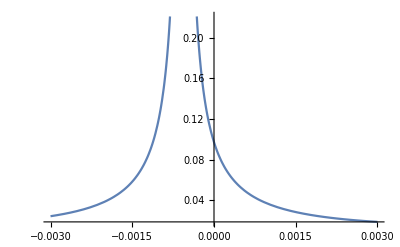

```mathematica
(*test with Plots*)
DelPhiPlot[g_, α1_, α2_, Γ_, r_, ϕ_, θ1_, θ2_] = LowerDelPhi;
Plot[Abs[DelPhiPlot[2, 3, 2, 0, 2, ϕ, Pi/2, 0]], {ϕ,-.003, .003}] 
(*This shows that changing theta1 phase does not help*)
```

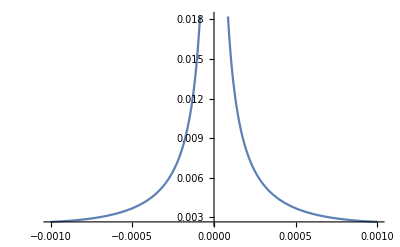

```mathematica
Plot[Abs[DelPhiPlot[2, 3, 2, 0, 2, ϕ, 0, 0]], {ϕ,-.001, .001}]
(* This looks good, try looking at the Full Range*)
```

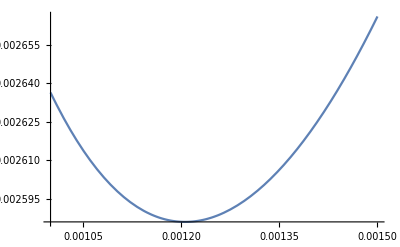

```mathematica
Plot[Abs[DelPhiPlot[2, 3, 2, 0, 2, ϕ, 0, 0]], {ϕ,0.0010, .0015}]
(*For the particular choice of alpha1 and alpha2, this point around 0.0010 looks minimum*)
(*In next plot, we look at other case, varying alpha*)
```

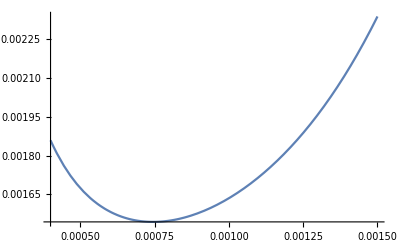

```mathematica
(*Let us look at the effect of changing alpha1 on total DelPHi*)
Plot[Abs[DelPhiPlot[2, 5, 2, 0, 2, ϕ, 0, 0]], {ϕ, .00040, 0.0015}]
(*Ok with alpha1 =5, we see that it has shifted a little bit to the origin*)
```

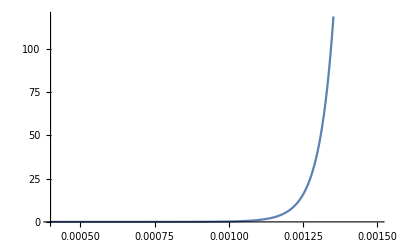

```mathematica
Plot[Abs[DelPhiPlot[2, 20, 2, 0, 2, ϕ, 0, 0]], {ϕ, .00040, 0.0015}]
(*Ok with the more increase in alpha1, the things blow up, can this be reduced with increasing alpha2 ? , the next plot checks this*)
```

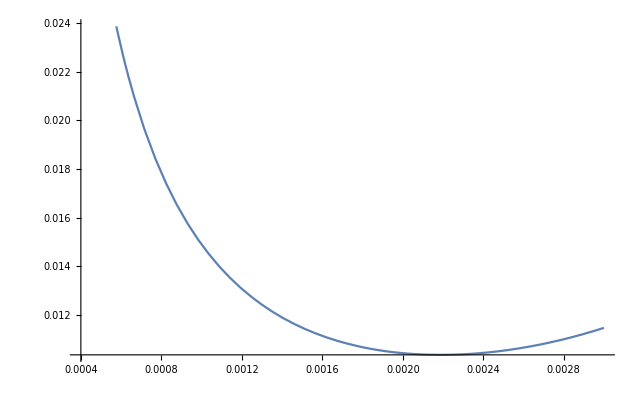

```mathematica
Plot[Abs[DelPhiPlot[2, 2, 5, 0, 2, ϕ, 0, 0]], {ϕ, .00040, 0.003}]
(*OK now changing alpha2, the minimum point is shifting to the right. For example, here with alpha2=5, the minimum looks around .002*)
```

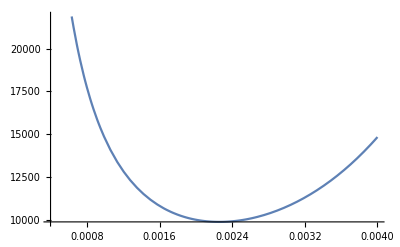

```mathematica
(*The above graph is also showing that increasing alpha more causes issue, it looks like sensitivity is going bad*, let's check in extreme case with large 
alpha2 *)
Plot[Abs[DelPhiPlot[2, 2, 20, 0, 2, ϕ, 0, 0]], {ϕ, .00040, 0.004}]
(*So, with increase in alpha 2 sensitivy is worsen*) 
(*Can it be that optimal startegy is similar to Dong Li's where you need similar photon number in both modes, let's check that*)
```

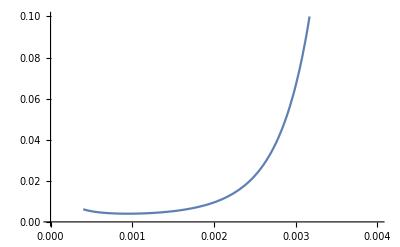

```mathematica
(*Let's put 5 alpha on first mode and 5 alpha in second and check*)
Plot[Abs[DelPhiPlot[2, 5, 5, 0, 2, ϕ, 0, 0]], {ϕ, .00040, 0.004}, PlotRange->{0,.1}]
```

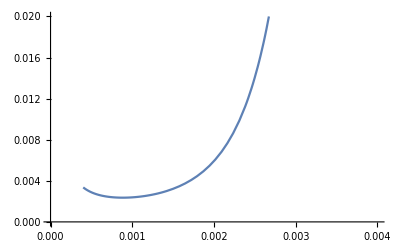

```mathematica
(*Is it that average equal photons are required on each mode like dong li, so alpha2 should be smaller than alpha1 because from squeezer itself, we have 13 photons*)
Plot[Abs[DelPhiPlot[2, 5, 3.5, 0, 2, ϕ, 0, 0]], {ϕ, .00040, 0.004}, PlotRange->{0,.02}]
```

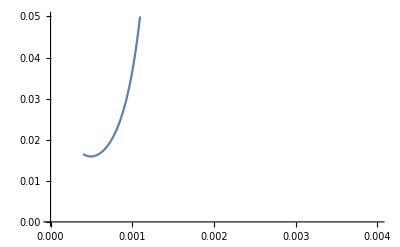

```mathematica
Plot[Abs[DelPhiPlot[2, 10, 9, 0, 2, ϕ, 0, 0]], {ϕ, .00040, 0.004}, PlotRange->{0,.05}]
```

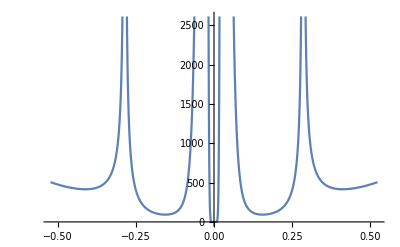

```mathematica
Plot[Abs[DelPhiPlot[2, 3, 2, 0, 2, ϕ, 0, 0]], {ϕ,-Pi/6, Pi/6}]
```

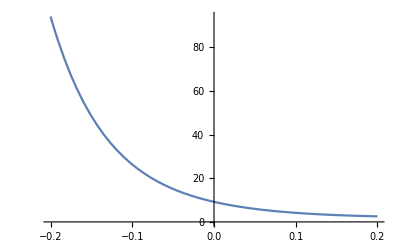

```mathematica
Plot[Abs[DelPhiPlot[2, 3, 2, Γ , 2, .1, Pi/4, Pi/4]], {Γ,-.2, .2}]
(*Ok the Γ=0 is very close to the optimal case*)
```

```mathematica
DelPhiWithZeroAngles = LowerDelPhi /. {Γ-> 0, θ1->0, θ2-> 0};
FinalDelPhiWithoutAngles[g_, α1_, α2_, r_, ϕ_] = DelPhiWithZeroAngles ;
```

```mathematica
(*Let's think about the actual plot for the paper, Let's put alpha1=5, alpha2=3.5, which will make average photon number on both port equal*)
Plot[Abs[DelPhiPlot[2, 5, 3.5, 0, 2, ϕ, 0, 0]], {ϕ, .00040, 0.004}, PlotRange->{0,.02}]
(*So the minimum is around phi= 0.001*)
```

-Graphics-

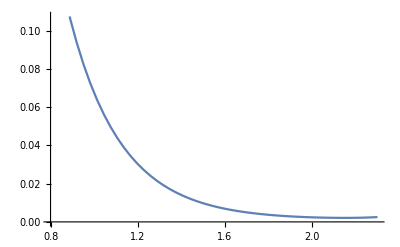

```mathematica
(*Plot Delta phi as a function of g*)
a = Plot[Abs[DelPhiPlot[g, 5, 3.5, 0, 2, 0.001, 0, 0]], {g, 0.8, 2.3}]
```

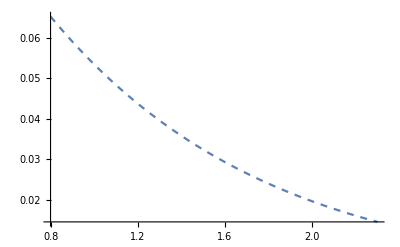

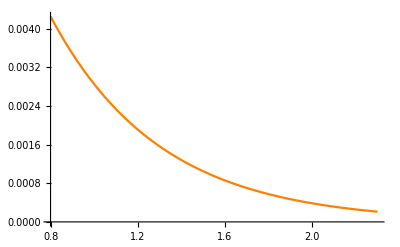

```mathematica
(*Plot the SNL and HL from DSV paper*)
snl = 1/Sqrt[((α2^2+Sinh[r]^2+α1^2)*(2*Sinh[g]^2+1) + 2*Sinh[g]^2 + 4*Sqrt[(1-Sinh[r]^2/(α2^2+Sinh[r]^2))α2^2+Sinh[r]^2]*α1*Sinh[g]Cosh[g] )];
Heigen = 1/((α2^2+Sinh[r]^2+α1^2)*(2*Sinh[g]^2+1) + 2*Sinh[g]^2 + 4*Sqrt[(1-Sinh[r]^2/(α2^2+Sinh[r]^2))α2^2+Sinh[r]^2]*α1*Sinh[g]Cosh[g] );
HeigenPlot[α1_, α2_, r_, g_ ] = Heigen;
snlPlot[α1_, α2_, r_, g_ ] = snl;
b = Plot[snlPlot[5, 3.5, 2, g], {g,.8,2.3}, PlotStyle->Dashed]
c = Plot[HeigenPlot[5, 3.5, 2, g], {g,.8,2.3},PlotStyle->Orange]
```

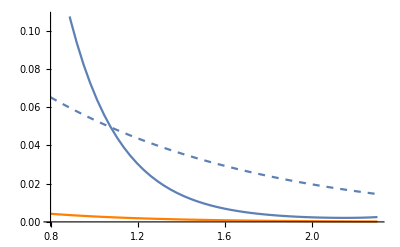

```mathematica
Show[a,b,c]
```

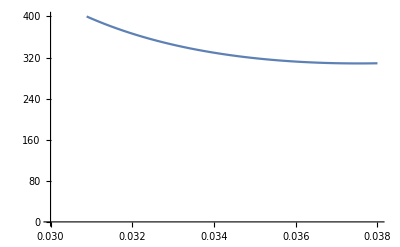

```mathematica
(*The increase in g doesn't help as can be seen here with g=3, its fucked up*)
Plot[Abs[DelPhiPlot[3, 5, 3.5, 0, 2, ϕ, 0, 0]], {ϕ, 0.030, .038}, PlotRange-> {0,400}]
```

```mathematica
(*Let's check if giving different phases in g=3 helps to get better sensitivity*)
Plot[Abs[DelPhiPlot[3, 5, 3.5, Pi/2, 2, ϕ, Pi/4, Pi/4]], {ϕ, 0.02, .05}]
```

-Graphics-

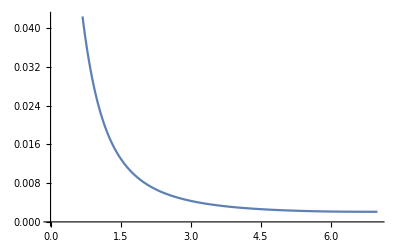

```mathematica
Plot[Abs[DelPhiPlot[2, α1, 3.5, 0, 2, 0.001,0, 0]], {α1, 0 ,7}]
(*This is 1 plot to keep*)
```